```mathematica
dir="D:\\newOutput"
```

D:\newOutput

```mathematica
cell=0;
GetAltitude[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
Cases[{"pt","y"}/.items,{cell,y_}->y]
]
```

```mathematica
GetAltitude[50000]
```

{0.015226,0.003151,0.012197,0.030909,0.,0.,0.0064,0.128679,0.034799,0.000566,1.21863,0.002572,0.109361,14597,9.13792,9.00951,10.4539,10.3693,4.34564,4.36242,4.3587,5.36145,5.36189,5.35087,6.36007,6.35162,6.34386}
 |  |  |  |

```mathematica
Needs["CUDALink`"]
```

```mathematica
fMin=10;
fMax=1932320;
df=10000;
yMax=100;
dy=1;
frames=Table[frame,{frame,fMin,fMax,df}];
data=ParallelMap[BinCounts[GetAltitude[#],{0,yMax,dy}]&,frames];
```

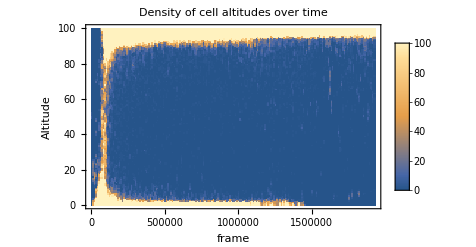

```mathematica
ListDensityPlot[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
FrameLabel->{"frame","Altitude"},
ClippingStyle->Automatic,
PlotRange->100,
PlotLegends->Placed[Automatic,Right],
InterpolationOrder->0,
AspectRatio->1/GoldenRatio,
PlotLabel->"Density of cell altitudes over time"
]
```

```mathematica
BinCounts[GetAltitude[fMax]]
```

{1,0,0,2,3,2,0,1,0,0,0,0,0,0,0,1,2,0,0,1,1,5,0,0,0,0,2,3,3,1,8,14,26,37,203,464,688,891,10162,9234,2499}

```mathematica
ListPlot3D[
data//Transpose,
DataRange->{{fMin,fMax},{0,yMax}},
AxesLabel->{"frame","Altitude"},
PlotRange->All,
ColorFunction->"DarkRainbow"]
```

-Graphics3D-